```mathematica
f[n_]:=If[n==1,Return[0],
	res=Mod[3^f[EulerPhi[n]],n];
	Return[res]
]
```

```mathematica
Timing[list=Table[f[i], {i, 2, 10000}];]
```

{0.61929,Null}

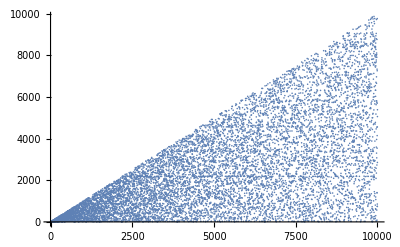

```mathematica
ListPlot[list]
```